### two-photon rabi flopping

P. Huft

## global definitions

```mathematica
Clear["Global`*"]
```

```mathematica
(*get from local files*)
SetDirectory[NotebookDirectory[]];
<<"rbconsts.m"
<<"physconsts.m"

(*CONSTANTS*)
ω780A =2414176448051179.0; (*5 Subscript[S, 1/2] F=2 -> 5 Subscript[P, 3/2] F=3*)
ω480 =3928955767695494.5;(*5 Subscript[P, 3/2] F=3 -> 84 Subscript[D, 5/2]*)
TFORT =1*^-3;(*[K]*)
λFORT=1.064*^-6;(*[m]*)
wFORT=2.5*^-6;(*[m]*)
ωrFORT =1/wFORT √((2 kB TFORT)/mRb);(*radial trap frequency*)
ωzFORT =λFORT/(π wFORT^2)√((2kB TFORT)/mRb) ;(*axial trap frequency*)
α780Ag=3.20346392953120*^-34;
α780Ae=1.52739309640219*^-34+-3.817491143122172*^-35+-4.5814576851206318*^-35;
α780Ar=-1.825469589864302*^-39; (* ponderomotive*)
α480g =-2.90311524481040*^-39;
α480e =-4.82150951678205*^-39+1.696626924053701*^-40+4.557481703934684*^-40;
α480r =-4.8350228219114005*^-39 (*ponderomotive*)

(*FUNCTIONS*)
AtomPositionSample[Tatom_]:={RandomVariate[NormalDistribution[0,1/ωrFORT √((kB Tatom)/mRb)]],
RandomVariate[NormalDistribution[0,1/ωrFORT √((kB Tatom)/mRb)]],
RandomVariate[NormalDistribution[0,1/ωzFORT √((kB Tatom)/mRb)]]};

BuildSchroedingerSystem[H_,psi0_]:=Module[
{hamiltonian=H,ψ0=psi0,ψ,statelength,eqs,ics,sys,P,i},
statelength = Length[ψ0];
ψ = Array[Subscript[P, #][t]&,statelength];
eqs = {};(*system to solve*)
ics = {};(*initial conditions*)
For[i=1,i<statelength+1,i++,
AppendTo[eqs,D[ψ[[i]],t]==-ⅈ (hamiltonian.ψ)[[i]]];
AppendTo[ics,(ψ[[i]]/.t->0)==ψ0[[i]]];
];
sys = Flatten@Join[eqs,ics];
{ψ,sys}
]

gJ[L_,J_]:=gL(J(J+1)+L(L+1)-S(S+1)
+gS(J(J+1)-L(L+1)+S(S+1)))/(2J(J+1));
gF[J_,F_]:= (gJ(F(F+1)+J(J+1)-INuc(INuc+1))
+gI(F(F+1)-J(J+1)+INuc(INuc+1)))/(2F(F+1));

(*Zeeman shifts, only for diagonal elements*)
FZeemanMatElem[L_,{J_,mJ_},{JJ_,mJJ_},Bz_]:=KroneckerDelta[mJ,mJJ] μB gJ[L,J]mJ Bz;
HFZeemanMatElem[I_,L_,J_,{F_,mF_},{FF_,mFF_},Bz_]:=KroneckerDelta[mF,mFF]μB Bz (ClebschGordan[{F,mF},{1,0},{FF,mFF}] √(2 F +1)(-1)^(1+J+I)(gJ[L,J] (-1)^F √(J (J+1)(2 J+1))SixJSymbol[{J,I,F},{FF,1,J}]+
gI(-1)^FF √(I(I+1)(2I+1))SixJSymbol[{I,J,F},{FF,1,I}]));

MaxBoltzVelocitySample[Tatom_]:={RandomVariate[MaxwellDistribution[√((kB Tatom)/mRb)]],
RandomVariate[MaxwellDistribution[√((kB Tatom)/mRb)]],
RandomVariate[MaxwellDistribution[√((kB Tatom)/mRb)]]};

intensityProfile[x_,y_,z_,zRx_,zRy_,zx_,zy_,wx_,wy_]:=Exp[(-2 x^2)/(wx^2(1+((z-zx)/zRx)^2))+(-2 y^2)/(wy^2(1+((z-zy)/zRy)^2))]/√((1+((z-zx)/zRx)^2)(1+((z-zy)/zRy)^2));(*Gaussian beam intensity profile*)
```

-4.83502×10^-39

## simple Rabi oscillation test

```mathematica
(*single atom Hamiltonian with effective basis {g,e}*)
Clear[Ω1,Ω2,Δ1,Δ2];
scl = 1*^9;
numStates=3; (*single atom states*)
numAtoms =1;
atomBasis = IdentityMatrix[numStates];
(*rabi frequencies and AC stark shifts calculated in rydberg_rabi.ipynb*)
Ω1=695214755.6324366; 
Ω2 = 71550273.89520717;
ΩEff = 2π*600099;
Δ1 = -13194689145.077131;
Δ2 =-Δ1;
diffACStarkHFge =1298349.0058336519;
diffACStarkHFer=339133.4042641225;
(*Haf=({{0, Ω1/2, 0}, {Ω1/2, Δ1 +diffACStarkHFge, Ω2/2}, {0, Ω2/2, (Δ1+diffACStarkHFge + Δ2 +diffACStarkHFer)}})/scl;*)
scl=1;
Ω1 = 1;Ω2=0.3;Δ1=20Ω1;Δ2=-Δ1;Γ=0;(*diagnostics, e.g. reproduce Shore examples*)

Haf=({{0, Ω1/2, 0}, {Ω1/2, Δ1, Ω2/2}, {0, Ω2/2, Δ1+Δ2+ⅈ Γ/2}})/scl;
ΩEff = Ω1 Ω2/(2Δ1);

(*assume real Rabi freq.*)
(*scl=1;
Haf=({{0, /2, 0}, {1/2, 0, 1/2}, {0, 1/2, 0}});(*Shore, page 794 Fig. 13.3-1*)
ΩEff = 1/(2*5);*)
Haf//MatrixForm
```

(0 | 1/2 | 0
1/2 | 20 | 0.15
0 | 0.15 | 0)

Time to run sim: 0 mins

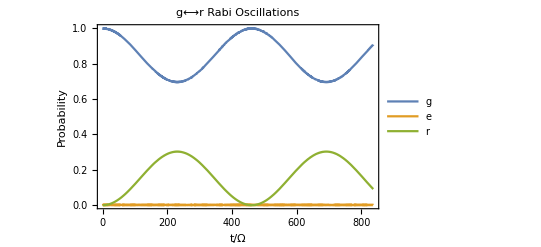

```mathematica
(*Build the initial array state and eqs to solve*)
ψ0 = ConstantArray[0,numAtoms numStates];
ψ0[[1]]=1;(*start with all atoms in ground state*)
tmax=2π scl/ΩEff;
{ψ,sys}=BuildSchroedingerSystem[Haf,ψ0];
{time,soln}= Timing[First@NDSolve[sys, ψ, {t,0,tmax},Method->"BDF"]];
Print[StringForm["Time to run sim: `` mins",Floor[time/60//N]]];
soln = Table[soln[[i,2]],{i,Range[Length[soln]]}];
leg = {"g","e","r"};
plt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2},{t,0,tmax},PlotLegends->leg,PlotLabel-> Style[StringForm["g⟷r Rabi Oscillations"],Black,FontSize->14],LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All]
```

## frequency scan. RIN, finite T

Run each cell below.

```mathematica
scl = 1*^9;(*time scale factor. multiply times, divide frequencies*)
```

### RIN data

```mathematica
(*780A RIN. todo: bundle setup stuff into function*)
VDC780A=0.310;
fname="srs_filtercav_noise_eaten_rin_20201223.asc";
contents=Import[fname,"Table"];
header =contents[[14]];
{HzPts780A,dBVpkPts780A}=Transpose@contents[[15;;-1]];
dBVpkPts780A-=10Log10[VDC780A];
(*to-do: set seed*)
phases =Array[RandomReal[]&,Length[dBVpkPts780A]];(*make phases pre-determined and same run-to-run of the simulation below*)
RIN780A[t_]:=1+Total[Array[Sqrt[10^(dBVpkPts780A[[#]]/10)]Cos[2π (HzPts780A[[#]]t/scl+phases[[#]])]&,Length[dBVpkPts780A]]];(*divide time by scl because time window in solver is mult. by scl. need to cancel to get real time*)
```

### Beams and differential frequency shifts

```mathematica
Clear[Ω1,Ω2,Δ1,Δ2,diffACStarkHFge,diffACStarkHFer];
numStates=3; (*single atom states*)
numAtoms =1;
atomBasis = IdentityMatrix[numStates];
(*rabi frequencies calculated in rydberg_rabi.ipynb*)
Δ1 = -2π*2100000000; (*780 detuning rad/s*)
Δ2 =-Δ1;(*480 detuning rad/s*)
λ780A = 2π c/(ω780A+Δ1);
λ480 =2π c/(ω480+Δ2);

fieldProfile780A[x_,y_,z_]:=√intensityProfile[x,y,z,(π (6*^-6)^2)/λ780A,(π (8*^-6)^2)/λ780A,0,2.2*^-4,6*^-6,8*^-6];
fieldProfile480[x_,y_,z_]:=√intensityProfile[x,y,z,(π (4*^-6)^2)/λ480,(π (4*^-6)^2)/λ780A,0,0,4*^-6,4*^-6];

Ω1[x_,y_,z_,t_]:=2π*102712885 fieldProfile780A[x,y,z] √RIN780A[t]; 
Ω2[x_,y_,z_,t_] := 2π*24538455 fieldProfile480[x,y,z];
ΩEff =(2π)^2*102712885 *24538455/(2Abs[Δ1]); 
ACStarkHFg[x_,y_,z_,t_] := -(α780Ag fieldProfile780A[x,y,z]^2 RIN780A[t]+α480g fieldProfile480[x,y,z]^2)/(4 ℏ);
ACStarkHFe[x_,y_,z_,t_] := -(α780Ae fieldProfile780A[x,y,z]^2 RIN780A[t]+α480e fieldProfile480[x,y,z]^2)/(4 ℏ);
ACStarkHFr[x_,y_,z_,t_] := -(α780Ar fieldProfile780A[x,y,z]^2 RIN780A[t]+α480r fieldProfile480[x,y,z]^2)/(4 ℏ);
diffACStarkHFge[x_,y_,z_,t_]:=ACStarkHFe[x,y,z,t]-ACStarkHFg[x,y,z,t];
diffACStarkHFer[x_,y_,z_,t_]:=ACStarkHFr[x,y,z,t]-ACStarkHFe[x,y,z,t];
Bbias = 3.6*10^-4 ;(*magnetic bias field [T]*)
diffZ1ge =(HFZeemanMatElem[INuc,1,3/2,{3,1},{3,1},Bbias]-HFZeemanMatElem[INuc,0,1/2,{2,0},{2,0},Bbias])/ℏ;
diffZ1er =(FZeemanMatElem[2,{5/2,5/2},{5/2,5/2},Bbias]-HFZeemanMatElem[INuc,1,3/2,{3,1},{3,1},Bbias])/ℏ;
dUge[x_,y_,z_,t_]:=diffACStarkHFge[x,y,z,t] + diffZ1ge;
dUer[x_,y_,z_,t_]:=diffACStarkHFer[x,y,z,t] + diffZ1er;
```

```mathematica
InitializeRINDependentQuantities[]:=(
phases =Array[RandomReal[]&,Length[dBVpkPts780A]];
RIN780A[t_]:=1+Total[Array[Sqrt[10^(dBVpkPts780A[[#]]/10)]Cos[2π (HzPts780A[[#]]t/scl+phases[[#]])]&,Length[dBVpkPts780A]]];
Ω1[x_,y_,z_,t_]:=2π*102712885 fieldProfile780A[x,y,z] √RIN780A[t]; 
Ω2[x_,y_,z_,t_] := 2π*24538455 fieldProfile480[x,y,z];
ΩEff =(2π)^2*102712885 *24538455/(2Abs[Δ1]); 
ACStarkHFg[x_,y_,z_,t_] := -(α780Ag fieldProfile780A[x,y,z]^2 RIN780A[t]+α480g fieldProfile480[x,y,z]^2)/(4 ℏ);
ACStarkHFe[x_,y_,z_,t_] := -(α780Ae fieldProfile780A[x,y,z]^2 RIN780A[t]+α480e fieldProfile480[x,y,z]^2)/(4 ℏ);
ACStarkHFr[x_,y_,z_,t_] := -(α780Ar fieldProfile780A[x,y,z]^2 RIN780A[t]+α480r fieldProfile480[x,y,z]^2)/(4 ℏ);
diffACStarkHFge[x_,y_,z_,t_]:=ACStarkHFe[x,y,z,t]-ACStarkHFg[x,y,z,t];
diffACStarkHFer[x_,y_,z_,t_]:=ACStarkHFr[x,y,z,t]-ACStarkHFe[x,y,z,t];
Bbias = 3.6*10^-4 ;(*magnetic bias field [T]*)
diffZ1ge =(HFZeemanMatElem[INuc,1,3/2,{3,1},{3,1},Bbias]-HFZeemanMatElem[INuc,0,1/2,{2,0},{2,0},Bbias])/ℏ;
diffZ1er =(FZeemanMatElem[2,{5/2,5/2},{5/2,5/2},Bbias]-HFZeemanMatElem[INuc,1,3/2,{3,1},{3,1},Bbias])/ℏ;
dUge[x_,y_,z_,t_]:=diffACStarkHFge[x,y,z,t] + diffZ1ge;
dUer[x_,y_,z_,t_]:=diffACStarkHFer[x,y,z,t] + diffZ1er;
);
```

```mathematica
"g-e differential Zeeman shift"
diffZ1er
"e-r differential Zeeman shift"
diffZ1ge
```

g-e differential Zeeman shift

7.37832×10^7

e-r differential Zeeman shift

2.10612×10^7

### Run

possible methodological issue: effects from fast frequencies in the time series RIN will not be resolved unless the time step size in the solver is < 1/f_fast

```mathematica
(*Build the initial array state and eqs to solve*)
ψ0 = ConstantArray[0,numAtoms numStates];
ψ0[[1]]=1;(*start with all atoms in ground state*)
tmax=π scl/ΩEff;
fTable= Table[2π fMHz*1*^6,{fMHz,Range[-16,-3,.2]}];
TTable ={0,50,100}/(1*^6);
solnList = {};
endPts = {};
measurements = 50;
Clear[j,i]
runtime=Timing[For[j=1,j<Length[TTable]+1,j++,
T=TTable[[j]];(*atom temp*)
endPts = {};
linetime=Timing[For[i=1, i<Length[fTable]+1,i++,

(*on each frequency step need to recalculate the RIN time series and parameters that depend on it*)
InitializeRINDependentQuantities[];

f =fTable[[i]];(*780 frequency tuning*)
time=0;
avgsNum =If[T≠0,measurements,1];
{x,y,z}=If[T≠ 0,AtomPositionSample[T],{0,0,0}];
{vx,vy,vz}=If[T≠ 0,MaxBoltzVelocitySample[T],{0,0,0}];
r[t_]:={x+vx t/scl,y+vy t/scl,z+vz t/scl};
args[t_]:=Join[r[t],{t}];
endPt = 0;(*the average loop gets a single data point*)
For[avgstep=1,avgstep<avgsNum+1,avgstep++,
Haf[t_]:=
({{0, (Ω1@@args[t])/2, 0}, {(Ω1@@args[t])/2, Δ1 + dUge @@args[t]+f, (Ω2@@args[t])/2}, {0, (Ω2@@args[t])/2, Δ1+dUge@@args[t] + Δ2 +dUer@@args[t]+ f}})/scl;
(*Print["building hamiltonian"];*)
{ψ,sys}=BuildSchroedingerSystem[Haf[t],ψ0];
(*Print["solving system"];*)
result= Timing[First@NDSolve[sys, ψ, {t,0,tmax}]];
time += result[[1]];
soln=result[[2]];
endPt+=(soln[[1,2]]/.t-> tmax)/avgsNum;
(*Print[StringForm["solved system in `` mins",Floor[time/60//N],NumberForm[time/60//N,2]]];*)
];
AppendTo[endPts,endPt];
];][[1]];

Print[StringForm["ran step T=`` μK in `` mins",T/(1*^6),If[time>60,Floor[linetime/60//N],NumberForm[linetime/60//N,2]]]];

AppendTo[solnList,endPts];
];
][[1]];
Print[StringForm["Total run time `` mins",If[runtime>60,Floor[runtime/60//N],NumberForm[runtime/60//N,2]]]]
```

ran step T=0 μK in 6.2 mins

$Aborted

Total run time 1 mins

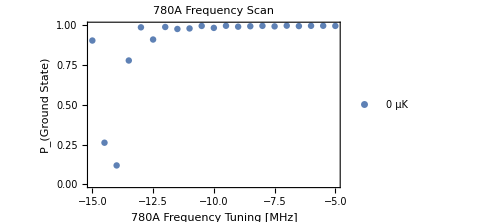

```mathematica
populationData = Array[Transpose@{fTable/(2π 1*^6),Abs[solnList[[#]]]^2}&,Length[solnList]];
leg =Array[StringForm["`` μK",TTable[[#]](1*^6)]&,Length[TTable]];
plt=ListPlot[populationData,PlotRange->{0,1},PlotLegends->leg,Frame->{True,True,False,False},Axes->False,PlotLabel->Style["780A Frequency Scan",FontSize-> 16],ImageSize->Medium,FrameLabel-> {"780A Frequency Tuning [MHz]","P_(Ground State)"},Axes-> False,LabelStyle-> Directive[Black,FontSize-> 14]]
```

```mathematica
(Δ1+dUge@@args[0] + Δ2 +dUer@@args[0])/(2π)
```

1.5095×10^7

```mathematica
(dUge@@args[0] )/(2π)
```

3.352×10^6

```mathematica
(dUer@@args[0])/(2π)
```

1.1743×10^7

```mathematica
(Δ1)/(2π)
```

-2100000000

```mathematica
(*fname="plot_rydberg_780Afrequency_scan_varied_0_50_75_100_uK.png";
Export[fname,plt]*)
(*fname="soln_rydberg_780Afrequency_scan_varied_0_50_75_100_uK.csv";
Export[fname,Transpose@Join[{fTable},solnList]]*)
```

plot_rydberg_780Afrequency_scan_varied_0_50_75_100_uK.png

step 0, 0.007 mins

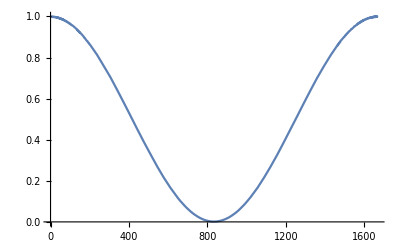

```mathematica
(*to show Rabi oscillation. need to edit to look at slices of populationData instead*)
fRedDetuning =2π scl  Sort[populationData,#1[[2]]<#2[[2]]&][[1,1]] ;
```

## misc testing

#### RIN data to time series

780A RIN data, post-noise eater

```mathematica
VDC=0.310;
fname="srs_filtercav_noise_eaten_rin_20201223.asc";
contents=Import[fname,"Table"];
header =contents[[14]];
{HzPts,dBVpkPts}=Transpose@contents[[15;;-1]];
dBVpkPts-=10Log10[VDC];
RINData=Transpose@{HzPts,dBVpkPts};
```

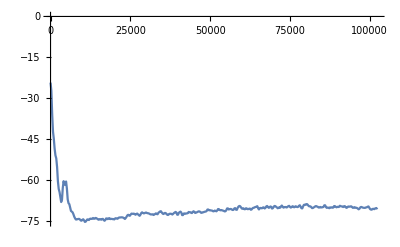

```mathematica
ListPlot[fdata,PlotRange->All,Joined->True]
```

```mathematica
timeRIN[t_]:=Total[Array[Sqrt[10^(dBVpkPts[[#]]/10)]Cos[2π (HzPts[[#]]t+RandomReal[])]&,Length[dBVpkPts]]];
```

```mathematica
timeRIN[0]
```

```mathematica
Re[0.12732698340348503+0.2240973466854182 ⅈ]
```

0.127327

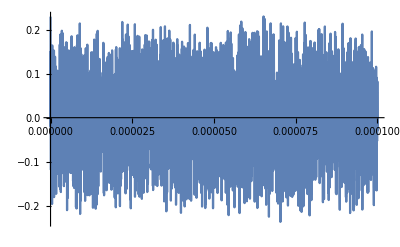

```mathematica
Plot[Re[timeRIN[t]],{t,0,0.0001},PlotRange->All]
```